# Finite Rod, Albedo Problem, Anisotropic Scattering

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2016 Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Exponential Random Flight

## Notation

α - single-scattering albedo
Σt - extinction coefficient
x - position coordinate in rod (source at x = 0)
a - length of the rod
g - ‘mean cosine’ of scattering
-Graphics-

## Analytic solutions

### Finite Rod Reflectance(R) and Transmittance(T)

```mathematica
Clear[α,g];
finiterodalbedoanisoscatter`R[a_,α_,Σt_,g_]:=((1-g) α)/(2-α-g α+2 √((1-α) (1-g α)) Coth[a √((1-α) (1-g α)) Σt])
```

```mathematica
finiterodalbedoanisoscatter`T[a_,α_,Σt_,g_]:=2/(2 Cosh[a √((1-α) (1-g α)) Σt]+((-2+α+g α) Sinh[-a √((1-α) (1-g α)) Σt])/(√((1-α) (1-g α))))
```

```mathematica
finiterodalbedoanisoscatter`R[a_,α_,Σt_,g_,n_]:=α^n(SeriesCoefficient[finiterodalbedoanisoscatter`R[a,A,Σt,g],{A,0,n}]/.A->α);
finiterodalbedoanisoscatter`T[a_,α_,Σt_,g_,n_]:=α^n(SeriesCoefficient[finiterodalbedoanisoscatter`T[a,A,Σt,g],{A,0,n}]/.A->α)
```

### ‘Radiance’

```mathematica
finiterodalbedoanisoscatter`LR[x_,α_,Σt_,a_,g_]:=-((ⅇ^(-(a+x) √((-1+α) (-1+g α)) Σt) √((-1+α)/(-1+g α)) (-2 √(-1+α) √(-1+g α) Cosh[(a-x) √(-1+α) √(-1+g α) Σt]+(-2+α+g α) Sinh[(a-x) √(-1+α) √(-1+g α) Σt]) (√(-1+α) √(-1+g α) Cosh[(a+x) √(-1+α) √(-1+g α) Σt]+√((-1+α) (-1+g α)) Sinh[(a+x) √(-1+α) √(-1+g α) Σt]))/((-1+α) (2 (-1+α) √((-1+g α)/(-1+α)) Cosh[a √((-1+α) (-1+g α)) Σt]+(-2+α+g α) Sinh[a √((-1+α) (-1+g α)) Σt])))
```

```mathematica
finiterodalbedoanisoscatter`LL[x_,α_,Σt_,a_,g_]:=(ⅇ^(-(a+x) √((-1+α) (-1+g α)) Σt) (ⅇ^(2 a √((-1+α) (-1+g α)) Σt)-ⅇ^(2 x √((-1+α) (-1+g α)) Σt)) √((-1+α)/(-1+g α)) (-√((-1+g α)/(-1+α))+g α √((-1+g α)/(-1+α))+√((-1+α) (-1+g α))))/(2 (2 (-1+α) √((-1+g α)/(-1+α)) Cosh[a √((-1+α) (-1+g α)) Σt]+(-2+α+g α) Sinh[a √((-1+α) (-1+g α)) Σt]))
```

### Fluence

```mathematica
finiterodalbedoanisoscatter`ϕ[x_,α_,Σt_,a_,g_]:=finiterodalbedoanisoscatter`LR[x,α,Σt,a,g]+finiterodalbedoanisoscatter`LL[x,α,Σt,a,g]
```

```mathematica
finiterodalbedoanisoscatter`ϕ[x_,α_,Σt_,a_,g_,n_]:=α^n(SeriesCoefficient[finiterodalbedoanisoscatter`ϕ[x,A,Σt,a,g],{A,0,n}]/.A->α);
```

## load MC data

```mathematica
finiterodalbedoanisoscatter`ppoints[xs_,dx_,maxx_,Σt_]:=Table[{dx(i-1)+0.5dx,(1/Σt)xs[[i]]},{i,1,Length[xs]}][[1;;-2]];
```

```mathematica
finiterodalbedoanisoscatter`fs=FileNames["code/rod/finiterod/albedoProblem/data/batch_finiterod_albedoproblem_anisotropicscatter_exp*"];
```

```mathematica
finiterodalbedoanisoscatter`index[x_]:=Module[{data,α,Σt,g,a},
data=Import[x,"Table"];
Σt=data[[1,11]];
α=data[[2,3]];
g=data[[1,-1]];
a=data[[2,5]];
{α,Σt,g,a,data}];
finiterodalbedoanisoscatter`simulations=finiterodalbedoanisoscatter`index/@finiterodalbedoanisoscatter`fs;
```

```mathematica
finiterodalbedoanisoscatter`alphas=Union[#[[1]]&/@finiterodalbedoanisoscatter`simulations]
```

{0.3,0.7,0.9}

```mathematica
finiterodalbedoanisoscatter`muts=Union[#[[2]]&/@finiterodalbedoanisoscatter`simulations]
```

{1,3}

```mathematica
finiterodalbedoanisoscatter`gs=Union[#[[3]]&/@finiterodalbedoanisoscatter`simulations]
```

{-0.5,0.3,0.7}

```mathematica
finiterodalbedoanisoscatter`as=Union[#[[4]]&/@finiterodalbedoanisoscatter`simulations]
```

{0.3,1,3}

```mathematica
finiterodalbedoanisoscatter`numcollorders=finiterodalbedoanisoscatter`simulations[[1]][[5]][[2,11]]
```

10

```mathematica
finiterodalbedoanisoscatter`nummoments=finiterodalbedoanisoscatter`simulations[[1]][[5]][[2,13]]
```

10

## Monte Carlo comparisons

```mathematica
fsplot1=FileNames["code/rod/finiterod/albedoProblem/data/finiterod_albedoproblem_anisotropicscatter_exp_c0.7_mut1_*"];
```

### Reflectance/Transmittance

```mathematica
MCR[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,5]];
{a,data[[3,4]]}
];
MCT[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,5]];
{a,data[[4,4]]}
]
```

```mathematica
Rs=Table[MCR[f],{f,fsplot1}];
Ts=Table[MCT[f],{f,fsplot1}];
```

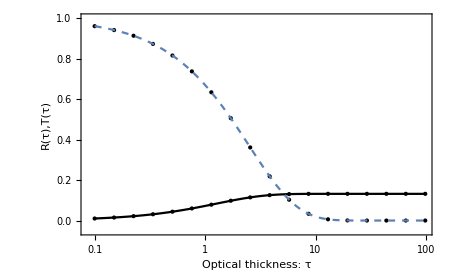

```mathematica
vizfiniterodRTaniso=Show[
ListLogLinearPlot[Rs,PlotRange->{-0.05,1},PlotStyle->{Black,PointSize[Medium]}],
ListLogLinearPlot[Ts,PlotRange->{-0.05,1},PlotStyle->{Black,PointSize[Medium]}],
LogLinearPlot[finiterodalbedoanisoscatter`R[a,0.7,1,0.7],{a,0.1,100},PlotStyle->Black],
LogLinearPlot[finiterodalbedoanisoscatter`T[a,0.7,1,0.7],{a,0.1,100},PlotStyle->Dashed],
ImageSize->450,
Frame->True,FrameLabel->{{"R(τ),T(τ)",},{"Optical thickness: τ","Total Reflectance/Transmittance (R/T): anisotropically-scattering finite rod (g = 0.7)"}}
]
```

```mathematica
fs2=FileNames["code/rod/finiterod/albedoProblem/data/finiterod_albedoproblem_anisotropicscatter_exp_*length2.6*"];
```

```mathematica
MCR2[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,3]];
{a,data[[3,4]]}
];
MCT2[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,3]];
{a,data[[4,4]]}
]
```

```mathematica
Rs2=Table[MCR2[f],{f,fs2}];
Ts2=Table[MCT2[f],{f,fs2}];
```

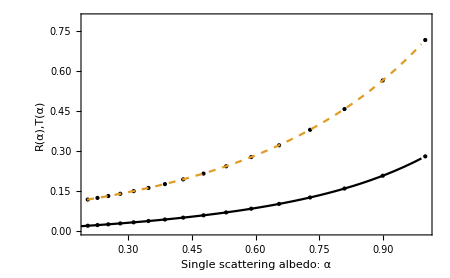

```mathematica
a=2.6;
mut=1;
finiterodvarycplot=Show[
ListPlot[Rs2,PlotRange->{0,0.8},PlotStyle->{Black,PointSize[Medium]}],
ListPlot[Ts2,PlotStyle->{Black,PointSize[Medium]}],
Plot[{finiterodalbedoanisoscatter`R[a,c,mut,0.7],finiterodalbedoanisoscatter`T[a,c,mut,0.7]},{c,0.01,.99},PlotRange->{0,1},PlotStyle->{Black,Dashed}],
ImageSize->450,
Frame->True,FrameLabel->{{"R(α),T(α)",},{"Single scattering albedo: α","Total Reflectance/Transmittance (R/T): anisotropically-scattering (g = 0.7) finite rod"}}
]
```

```mathematica
fs3=FileNames["code/rod/finiterod/albedoProblem/data/finiterod_albedoproblem_anisotropicscatter_exp_*length1.2*"];
```

```mathematica
MCR3[f_]:=Module[{data,g},
data=Import[f,"Table"];
g=data[[1,-1]];
{g,data[[3,4]]}
];
MCT3[f_]:=Module[{data,g},
data=Import[f,"Table"];
g=data[[1,-1]];
{g,data[[4,4]]}
]
```

```mathematica
Rs3=Table[MCR3[f],{f,fs3}];
Ts3=Table[MCT3[f],{f,fs3}];
```

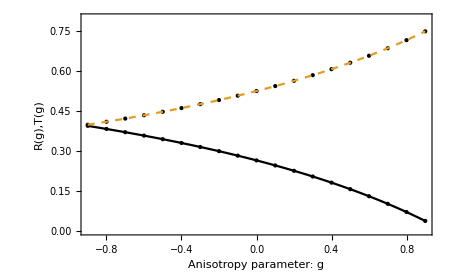

```mathematica
a=1.2;
mut=1;
c=0.8;
finiterodvarygplot=Show[
ListPlot[Rs3,PlotRange->{0,0.8},PlotStyle->{Black,PointSize[Medium]}],
ListPlot[Ts3,PlotStyle->{Black,PointSize[Medium]}],
Plot[{finiterodalbedoanisoscatter`R[a,c,mut,g],finiterodalbedoanisoscatter`T[a,c,mut,g]},{g,-0.9,0.9},PlotRange->{0,1},PlotStyle->{Black,Dashed}],
ImageSize->450,
Frame->True,FrameLabel->{{"R(g),T(g)",},{"Anisotropy parameter: g","Total Reflectance/Transmittance (R/T): anisotropically-scattering finite rod (c = 0.8, a = 1.2)"}}
]
```

### n-th collided Reflectance/Transmittance

```mathematica
Manipulate[
If[Length[finiterodalbedoanisoscatter`simulations]>0,
Module[{data,numcollorders,Rs,ns,analyticR,analyticT,Ts,j},
data=SelectFirst[finiterodalbedoanisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==g&&#[[4]]==a&][[5]];
numcollorders=data[[2,11]];
Rs=N[{data[[6]]}];
Ts=N[{data[[8]]}];
ns=Table[n,{n,0,numcollorders-1}];
analyticR=Table[finiterodalbedoanisoscatter`R[a,α,Σt,g,n],{n,ns}];
analyticT=Table[finiterodalbedoanisoscatter`T[a,α,Σt,g,n],{n,ns}];
j=Join[{ns},{analyticR},Rs,{analyticT},Ts];
TableForm[
Join[{{"n","R (analytic)","R (MC)","T (analytic)","T (MC)"}},Transpose[j]]
]
]
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{α,finiterodalbedoanisoscatter`alphas},{Σt,finiterodalbedoanisoscatter`muts},{g,finiterodalbedoanisoscatter`gs},{a,finiterodalbedoanisoscatter`as}]
```

### Internal Distributions

```mathematica
Manipulate[
If[Length[finiterodalbedoanisoscatter`simulations]>0,
Module[{data,numcollorders,nummoments,dx,pointsCL,plotpointsCL,pointsCR,plotpointsCR,plotpointsϕ,plotϕ,plotLL,plotLR},
data=SelectFirst[finiterodalbedoanisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==g&&#[[4]]==a&][[5]];
numcollorders=data[[2,11]];
nummoments=data[[2,13]];
dx=data[[2,7]];
pointsCL = data[[10]];
(* divide by Σt to convert collision density into L *)
plotpointsCL=finiterodalbedoanisoscatter`ppoints[pointsCL,dx,a,Σt];
pointsCR = data[[12]];
plotpointsCR=finiterodalbedoanisoscatter`ppoints[pointsCR,dx,a,Σt];
(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=finiterodalbedoanisoscatter`ppoints[pointsCL+pointsCR,dx,a,Σt];

plotϕ=Show[
ListPlot[plotpointsϕ,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[finiterodalbedoanisoscatter`ϕ[x,α,Σt,a,g],{x,0,a},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ[x],},{x,"Finite rod, albedo problem, anisotropic scattering, fluence ϕ[x]\n α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", a = "<>ToString[a]<>", g = "<>ToString[g]}}
];

plotLL=Show[
ListPlot[plotpointsCL,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[finiterodalbedoanisoscatter`LL[x,α,Σt,a,g],{x,0,a},PlotRange->All],
Plot[finiterodalbedoanisoscatter`ϕ[x,α,Σt,a,g],{x,0,a},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubMinus[L][x],},{x,"Finite rod, albedo problem, anisotropic scattering, L_-[x]\n α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", a = "<>ToString[a]<>", g = "<>ToString[g]}},PlotRange->All
];

plotLR=Show[
ListPlot[plotpointsCR,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[finiterodalbedoanisoscatter`LR[x,α,Σt,a,g],{x,0,a},PlotRange->All],
Plot[finiterodalbedoanisoscatter`ϕ[x,α,Σt,a,g],{x,0,a},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubPlus[L][x],},{x,"Finite rod, albedo problem, anisotropic scattering, L_+[x]\n α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", a = "<>ToString[a]<>", g = "<>ToString[g]}},PlotRange->All
];
GraphicsRow[{Show[plotϕ,ImageSize->400],plotLL,plotLR}]
]
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{α,finiterodalbedoanisoscatter`alphas},{Σt,finiterodalbedoanisoscatter`muts},{g,finiterodalbedoanisoscatter`gs},{a,finiterodalbedoanisoscatter`as}]
```

### Nth order fluence/density

```mathematica
Manipulate[
If[Length[finiterodalbedoanisoscatter`simulations]>0,
Module[{data,numcollorders,nummoments,dx,nthϕ,plotpointsϕ,plotϕ},
data=SelectFirst[finiterodalbedoanisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==g&&#[[4]]==a&][[5]];
numcollorders=data[[2,11]];
nummoments=data[[2,13]];
dx=data[[2,7]];

nthϕ=data[[16+numcollorders+1;;16+2numcollorders]];
plotpointsϕ=finiterodalbedoanisoscatter`ppoints[nthϕ[[n+2]],dx,a,Σt];

plotϕ=Show[
ListPlot[plotpointsϕ,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[finiterodalbedoanisoscatter`ϕ[x,α,Σt,a,g,n],{x,0,a},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ[x|n],},{x,"Finite rod, albedo problem, anisotropic scattering, fluence ϕ[x|n]\n α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", a = "<>ToString[a]<>", g = "<>ToString[g]}}
];


plotϕ
]
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{α,finiterodalbedoanisoscatter`alphas},{Σt,finiterodalbedoanisoscatter`muts},{g,finiterodalbedoanisoscatter`gs},{a,finiterodalbedoanisoscatter`as},
{{n,4},Range[If[NumberQ[finiterodalbedoanisoscatter`nummoments],finiterodalbedoanisoscatter`nummoments,1]]}
]
```